Hydrodynamical model of QED cascade expansion in an extremely strong laser pulse

Paper: Samsonov et al, Matter Radiat. Extremes 6, 034401 (2021); https://doi.org/10.1063/5.0035347
Notebook: Óscar Amaro, March 2023 @ GoLP-EPP

Introduction
We compare this notebook’s implementation with data retrieved from the paper (with WebPlotDigitizer).

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Figure 10

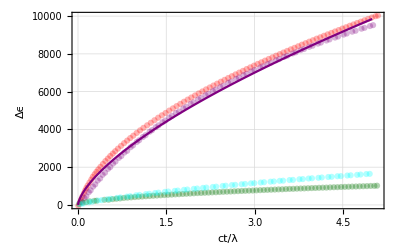

```mathematica
Clear[a0,p0,θ,μ,ctλ,ϵ0,Δϵacc,dataJoined]
a0=2500;
p0=500;
θ=π;
μ=ctλ/3;
ϵ0=Sqrt[1+p0^2];
Δϵacc=(55μ^2)^(1/3) a0^(2/3) ϵ0^(1/3) (1-Cos[θ])^(1/3);
dataJoined=False;
Show[{
ListPlot[Import["data/fig10_Deacc.csv"],Joined->dataJoined,PlotStyle->{Red,Opacity[0.3]},GridLines->Automatic,Frame->True,FrameLabel->{"ct/λ","Δϵ"},PlotRange->{0,10000}],
ListPlot[Import["data/fig10_DeaccApprox.csv"],Joined->dataJoined,PlotStyle->{Dashed,Purple,Opacity[0.3]}],ListPlot[Import["data/fig10_Derad.csv"],Joined->dataJoined,PlotStyle->{Darker[Darker[Green]],Opacity[0.3]}],
ListPlot[Import["data/fig10_DeradApprox.csv"],Joined->dataJoined,PlotStyle->{Dashed,Cyan,Opacity[0.3]}],
Plot[Δϵacc,{ctλ,0,5},PlotStyle->Directive[Purple]]}]
```

## Figure 11

```mathematica
Clear[vx,np,ν,Ε,sols,S]
sols=Solve[1/vx==Sqrt[1+(2np ν)/Ε Sqrt[1-vx^2]],vx]//Simplify
S=4np ν/Ε;(sols[[5,1,2]]^2-(2/(1+Sqrt[1+S^2])))//FullSimplify
(* they are the same expression *)
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{vx→1},{vx→-(√(-(Ε^2+√(Ε^4+16 np^2 Ε^2 ν^2))/(np^2 ν^2)))/(2 √2)},{vx→(√(-(Ε^2+√(Ε^4+16 np^2 Ε^2 ν^2))/(np^2 ν^2)))/(2 √2)},{vx→-(√((-Ε^2+√(Ε^4+16 np^2 Ε^2 ν^2))/(np^2 ν^2)))/(2 √2)},{vx→(√((-Ε^2+√(Ε^4+16 np^2 Ε^2 ν^2))/(np^2 ν^2)))/(2 √2)}}

(-Ε^2 √(1+(16 np^2 ν^2)/Ε^2)+√(Ε^4+16 np^2 Ε^2 ν^2))/(8 np^2 ν^2)

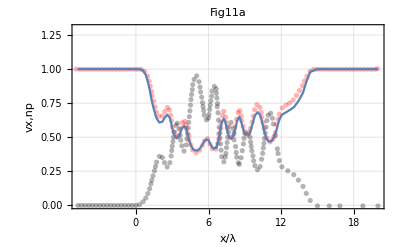

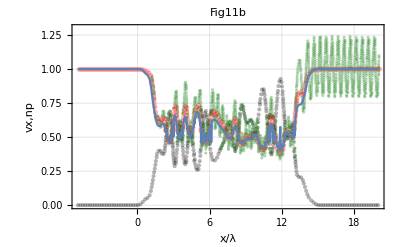

```mathematica
Clear[dataJoined,ν,S,np,Ε]
ν=1;(* ν^2=1 *)
vx = Sqrt[2/(1+Sqrt[1+S^2])];(* (B17) *)
S=4np ν/Ε;(* (B18) *)
Ε=1/3;(* value of Ε is not explicit in text *)

dataJoined=False;
npX=Import["data/fig11a_np.csv"][[All,1]];
np=Import["data/fig11a_np.csv"][[All,2]];
Show[{ListPlot[Import["data/fig11a_np.csv"],Joined->dataJoined,PlotStyle->{Black,Opacity[0.3]},GridLines->Automatic,Frame->True,FrameLabel->{"x/λ","vx,np"},PlotRange->{0,1.3},PlotLabel->"Fig11a"],ListPlot[Import["data/fig11a_approx.csv"],Joined->dataJoined,PlotStyle->{Red,Opacity[0.3]}],ListPlot[Transpose[{npX,vx}],Joined->True]}]

Clear[np,npX]
npX=Import["data/fig11b_np.csv"][[All,1]];
np=Import["data/fig11b_np.csv"][[All,2]];
Show[{ListPlot[Import["data/fig11b_np.csv"],Joined->dataJoined,PlotStyle->{Black,Opacity[0.3]},GridLines->Automatic,Frame->True,FrameLabel->{"x/λ","vx,np"},PlotRange->{0,1.3},PlotLabel->"Fig11b"],ListPlot[Import["data/fig11b_approx.csv"],Joined->dataJoined,PlotStyle->{Red,Opacity[0.3]}],ListPlot[Import["data/fig11b_vx.csv"],Joined->dataJoined,PlotStyle->{Darker[Darker[Green]],Opacity[0.3]}],ListPlot[Transpose[{npX,vx}],Joined->True]}]
```